```mathematica
β[ω_,δ_,t_,ϵ_,m_]:=
β[ω,δ,t,ϵ,m]=ReplacePart[(ω+ⅈ*δ-ϵ)IdentityMatrix[2m],Join[Table[{i,i-1},{i,Range[2,2m,1]}],Table[{i,i+1},{i,Range[1,2m,1]}],Table[{2n-1,2m-2n+2},{n,(m+1)/2}],Table[{2m-2n+2,2n-1},{n,(m-1)/2}]]->-t]
```

```mathematica
T1[t_,m_]:=T1[t,m]=ReplacePart[0*IdentityMatrix[2m],Table[{2n,2m-2n+1},{n,(m-1)/2}]->t]
```

```mathematica
ρ[t_,m_]:=ReplacePart[0*IdentityMatrix[2m],Table[{2n,2n},{n,(m-1)/2}]->t]
```

```mathematica
Clear[LEFT,SR]
```

```mathematica
Leads=Table[ToExpression[Import["/home/shardulmukim/PhD/fwi/AGNR/7AGNR/Leads/lead_"<>ToString[X]<>".dat"]],{X,Range[0,3,0.01]}]
```

{1}
 |  |  |  |

```mathematica
LEFT[ω_,δ_,t_,ϵ_,m_]:=LEFT[ω,δ,t,ϵ,m]=Leads[[ω*100+1]]
```

```mathematica
g[ω_,δ_,t_,ϵ_,m_]:= Inverse[β[ω,δ,t,ϵ,m]]
```

```mathematica
SR[ω_,δ_,t_,ϵ_,m_]:=SR[ω,δ,t,ϵ,m]=Inverse[IdentityMatrix[2m]-g[ω,δ,t,ϵ,m].T1[t,m].LEFT[ω,δ,t,ϵ,m].T1[t,m]].g[ω,δ,t,ϵ,m]
```

```mathematica
Clear[SL]
```

```mathematica
SL[ω_,δ_,t_,ϵ_,m_]:=SL[ω,δ,t,ϵ,m]=LEFT[ω,δ,t,ϵ,m]
```

```mathematica
IL[ω_,δ_,t_,ϵ_,m_]:=Inverse[IdentityMatrix[2m]-SL[ω,δ,t,ϵ,m].ρ[t,m].LEFT[ω,δ,t,ϵ,m].ρ[t,m]].SL[ω,δ,t,ϵ,m]
```

```mathematica
IR[ω_,δ_,t_,ϵ_,m_]:=Inverse[IdentityMatrix[2m]-LEFT[ω,δ,t,ϵ,m].ρ[t,m].SL[ω,δ,t,ϵ,m].ρ[t,m]].LEFT[ω,δ,t,ϵ,m]
```

```mathematica
gdd[ω_,δ_,t_,ϵ_,m_]:= IL[ω,δ,t,ϵ,m]-ConjugateTranspose[IL[ω,δ,t,ϵ,m]]
```

```mathematica
grr[ω_,δ_,t_,ϵ_,m_]:= IR[ω,δ,t,ϵ,m]-ConjugateTranspose[IR[ω,δ,t,ϵ,m]]
```

```mathematica
Gnonlocal[ω_,δ_,t_,ϵ_,m_]:= LEFT[ω,δ,t,ϵ,m].ρ[t,m].IL[ω,δ,t,ϵ,m]
```

```mathematica
GNON[ω_,δ_,t_,ϵ_,m_]:= Gnonlocal[ω,δ,t,ϵ,m]-ConjugateTranspose[Gnonlocal[ω,δ,t,ϵ,m]]
```

```mathematica
tr[ω_,δ_,t_,ϵ_,m_]:=Abs[Tr[gdd[ω,δ,t,ϵ,m].ρ[t,m].grr[ω,δ,t,ϵ,m].ρ[t,m]-ρ[t,m].GNON[ω,δ,t,ϵ,m].ρ[t,m].GNON[ω,δ,t,ϵ,m]]]
```

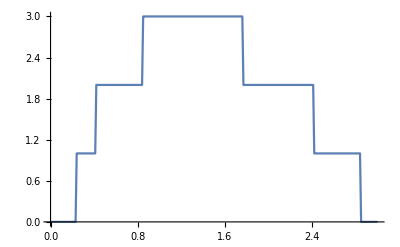

```mathematica
ListLinePlot[Table[{ω,tr[ω,0.0001,1,0,7]},{ω,Range[0,3,0.01]}]]
```

```mathematica
F[n_]:= {n,n}
```

```mathematica
unit[ω_,δ_,t_,ϵ_,ϵ1_,n_]:=Inverse[Module[{b=β[ω,δ,t,ϵ,7],F},(*F[ν_]:= {ν,ν};*)ReplacePart[b,(*Table[F[RandomSample[{RandomInteger[{1,14}]},1]]//Flatten,1]*){{n,n}}->ω+ⅈ*δ-ϵ1]]]
```

```mathematica
sl[ω_,ϵ1_,m_,x_]:= Module[{J=SL[ω,0.0001,1,0,m]},list={{unit[ω,0.0001,1,0,ϵ1,3],unit[ω,0.0001,1,0,ϵ1,10],unit[ω,0.0001,1,0,ϵ1,14],unit[ω,0.0001,1,0,ϵ1,6],unit[ω,0.0001,1,0,ϵ1,4]}};Do[J=Inverse[IdentityMatrix[2m]-list[[1,ζ]].ConjugateTranspose[T1[1,m]].J.T1[1,m]].list[[1,ζ]],{ζ,x}];
 J=J]
```

```mathematica
g66[ω_,ϵ1_,m_,x_]:= Inverse[IdentityMatrix[2m]-LEFT[ω,0.0001,1,0,7].ρ[1,m].sl[ω,ϵ1,m,5].ρ[1,m]].LEFT[ω,0.0001,1,0,7]
```

```mathematica
gfinal33[ω_,ϵ1_,m_,x_]:= sl[ω,ϵ1,7,3].(IdentityMatrix[2m]+T1[1,m].sl[ω,ϵ1,7,4].(ConjugateTranspose[T1[1,m]]+T1[1,m].sl[ω,ϵ1,7,5].(ConjugateTranspose[T1[1,m]]+ρ[1,m].g66[ω,ϵ1,7,5].ConjugateTranspose[ρ[1,m]].sl[ω,ϵ1,7,5].ConjugateTranspose[T1[1,m]]).sl[ω,ϵ1,7,4].ConjugateTranspose[T1[1,m]])).sl[ω,ϵ1,7,3]
```

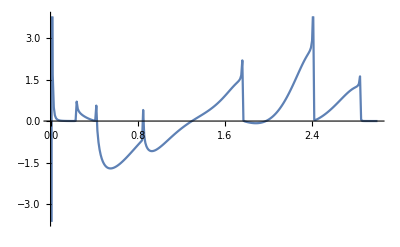

```mathematica
ListLinePlot[Table[{ω,-Im[gfinal33[ω,0,7,5][[2,2]]]},{ω,Range[0,3,0.01]}]]
```